```mathematica
V0=10;
ω=2π/(20*10^(-3));
```

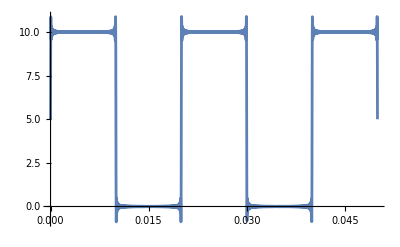

```mathematica
Plot[V0/2 + 2V0/Pi Sum[1/(2k+1)Sin[(2k+1)ω t],{k,0,100}],{t,0,50*10^(-3)}]
```

```mathematica
Plot[V0/2 + 2V0/Pi Sum[1/(2k+1)Re[-I Exp[I(2k+1)ω t]],{k,0,100}],{t,0,50*10^(-3)}]
```

-Graphics-

```mathematica
R=1;
L=1*10^(-3);
```

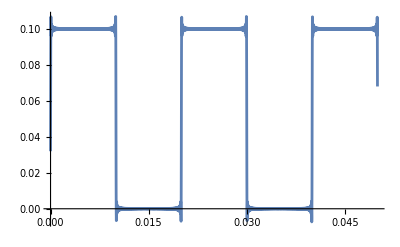

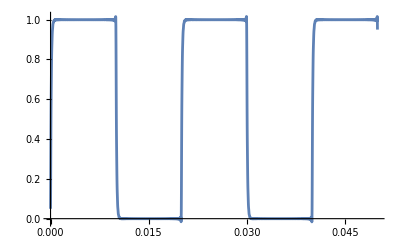

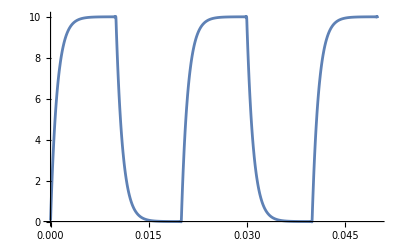

```mathematica
Plot[1/100 V0/2 + 2V0/Pi Sum[1/(2k+1)Re[1/(100+I (2k+1)ω L) (-I Exp[I(2k+1)ω t])],{k,0,100}],{t,0,50*10^(-3)}]
Plot[1/10 V0/2 + 2V0/Pi Sum[1/(2k+1)Re[1/(10+I (2k+1)ω L) (-I Exp[I(2k+1)ω t])],{k,0,100}],{t,0,50*10^(-3)}]
Plot[1/1 V0/2 + 2V0/Pi Sum[1/(2k+1)Re[1/(1+I (2k+1)ω L) (-I Exp[I(2k+1)ω t])],{k,0,100}],{t,0,50*10^(-3)}]
```